Leonid Shifrin

Mathematica programming: an advanced introduction                             < >    Ξ

Edited by Hao Feng

## Section | Introduction

Mathematica is built on a small number of universal principles. Good understanding of these principles is a pre-requisite for understanding how to program in Mathematica. Here I will discuss them, but rather briefly. Excellent and in-depth discussion of them can be found in several places [1, 2, 6-9].

### First principle: everything is an expression

The first principle states that every object dealt with by Mathematica, is an expression. Every Mathematica expression is either Atom, or a Normal Expression.

#### Atoms and the built-in AtomQ predicate

Atoms are numbers, symbols and strings, and numbers are further divided into Integers, Reals, Rationals and Complex. All other objects are composite and are called Normal Expressions. It is always possible to check whether or not an expression is an atom or a composite, by acting on it with the built-in predicate AtomQ. For instance:

```mathematica
ClearAll["Global'*"];
{AtomQ[x],AtomQ[Sin[x]],AtomQ[1+I*2],AtomQ[2/3]}
```

{True,False,True,True}

#### Mathematica normal (composite) expressions

Every normal expression (composite) is built according to a universal pattern:

```mathematica
expr[el1, ..., eln]
```

Here it is required that some symbol <expr> is present (it can itself be a normal expression, not necessarily an atom), as well as the single square brackets. Inside the square brackets, there can be zero, one or several comma-separated elements <el1>,...,<eln>. These elements themselves can be either atoms or normal expressions. In an expression Sin[x], <expr> is Sin, and there is a single element <x>, which is atom (as long as x is not defined as something else, but this already has to do with expression evaluation and will be discussed below). It is clear that an arbitrary Mathematica expression must have a tree-like structure, with the branches being normal (sub)expressions and leaves being atoms.

#### Literal equivalents of built-in functions, and FullForm command

As a consequence, any built-in command/function in Mathematica has a literal/string equivalent (so that it can be represented in the above uniform way). This is most easily seen with the help of the built-in function FullForm, which shows the internal representation of any object/expression, in the way it is really “seen” by the kernel. For instance:

```mathematica
{z*Sin[x+y],FullForm[z*Sin[x+y]]}
```

{z Sin[x+y],Times[z,Sin[Plus[x,y]]]}

The second expression in the curly braces is equivalent to the first one, but explicitly shows the structure described above.

#### All normal expressions are trees - TreeForm command

That it is a tree, can be seen most clearly with another built-in command TreeForm:

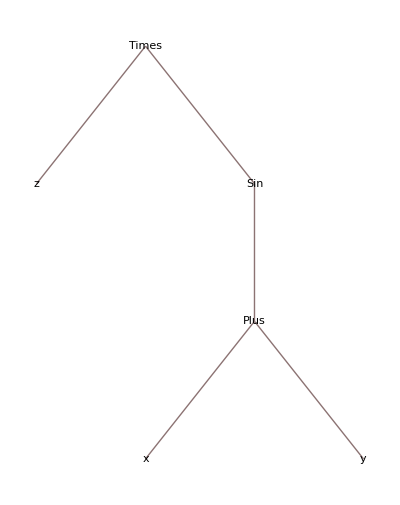

```mathematica
TreeForm[z*Sin[x+y]]
```

Since it is a tree, it is possible to index and access the subexpressions. In the following example <expr> is Times (the multiplication command):

```mathematica
a=z*Sin[x+y];
FullForm[a]
```

Times[z,Sin[Plus[x,y]]]

#### Heads of expressions and the Head command

In general, an expression outside the square brackets has a name - it is called a head of expression, or just head. There is a built-in function with the same name, which allows to obtain the head of an arbitrary expression. For example:

```mathematica
Head[a]
```

Times

A head of an expression may be either an atom or a normal expression itself. For example:

```mathematica
Clear[b,f,g,h,x];
b=f[g][h][x];
Head[b]
```

f[g][h]

```mathematica
Head[f[g][h]]
```

f[g]

```mathematica
Head[f[g]]
```

f

Every expression has a head, even atoms. Heads for them are String, Symbol, Integer, Real, Rational and Complex. For instance:

```mathematica
{Head[f],Head[2],Head[Pi],Head[3.14],Head["abc"],Head[2/3],Head[1+I]}
```

{Symbol,Integer,Symbol,Real,String,Rational,Complex}

#### Accessing individual parts of expressions through indexing

One can access also the internal parts of an expression (those inside the square brackets), by using indexing (Part command). The following example illustrates this.

```mathematica
{a[[0]],a[[1]],a[[2]],a[[2,0]],a[[2,1]],a[[2,1,0]],a[[2,1,1]],a[[2,1,2]]}
```

{Times,z,Sin[x+y],Sin,x+y,Plus,x,y}

We have just deconstructed our expression to pieces. In fact, we started from the “stem” and then went down along the “branches” to the “leaves” of the tree which we have seen above with the TreeForm. We see that the addresses (index sequences) which end with zero give the Heads of the subexpressions - this is a convention. In principle, any complex expression can be deconstructed in this way, and moreover, one can change its subexpressions.

#### Levels of expressions and the Level command

It is also possible to get access to the branches (subexpressions) which are the certain distance (level) from the “stem”. This is achieved by using a built-in Level command. Consider an example: certain distance (level)

```mathematica
Clear[a];
a=z*Sin[x+y]+z1*Cos[x1+y1]
```

z1 Cos[x1+y1]+z Sin[x+y]

Here is its full form:

```mathematica
FullFrom[a]
```

FullFrom[z1 Cos[x1+y1]+z Sin[x+y]]

Here is its tree form:

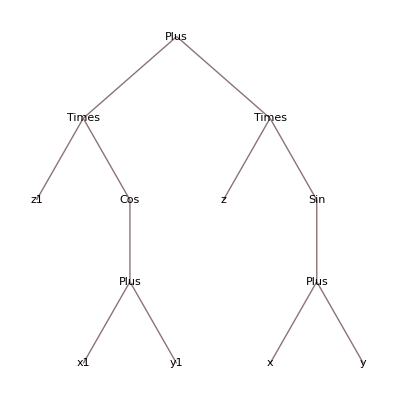

```mathematica
TreeForm[a]
```

And these are the levels of the tree:

```mathematica
Level[a,{0}]
Level[a,{1}]
Level[a,{2}]
Level[a,{3}]
Level[a,{4}]
```

{z1 Cos[x1+y1]+z Sin[x+y]}

{z1 Cos[x1+y1],z Sin[x+y]}

{z1,Cos[x1+y1],z,Sin[x+y]}

{x1+y1,x+y}

{x1,y1,x,y}

Level[a, {n}] gives all branches (or leaves) which have a distance of n levels down from the “stem”. If however we need all branches that have n levels of sub-branches (or leaves), then we use a negative level Level[a, {-n}]:

```mathematica
Level[a,{-1}]
Level[a,{-2}]
Level[a,{-3}]
Level[a,{-4}]
```

{z1,x1,y1,z,x,y}

{x1+y1,x+y}

{Cos[x1+y1],Sin[x+y]}

{z1 Cos[x1+y1],z Sin[x+y]}

Notice that negative levels generally can not be reduced to positive levels - they are giving in general different types of information. What we have just described is called the Standard Level Specification in Mathematica. Many more built-in commands accept level specification as one of the arguments (often an optional one).

Any function can be used also in its literal equivalent form. For instance:

```mathematica
{Plus[1,2,3,4],Times[1,2,3,4]}
```

{10,24}

### Second principle: pattern-matching and rule substitution

Another fundamental principle is so-called pattern-matching, which is a system to match rules and expressions - without it Mathematica would not know when to apply which rule. It is based on syntactic rather than semantic comparison of expressions. The main notions here are those of rules and patterns.

#### Rewrite Rules

```mathematica
Clear[a,b,c,d,e];
```

A typical rule looks like

```mathematica
a->b
```

where in general <a> and <b> are some Mathematica expressions. The rule just says: whenever <a> is encountered, replace it by <b>. For example:

```mathematica
{a,c,d,c}/.a->b
```

{b,c,d,c}

(the </.> symbol is a rule replacement command, to be covered later).

A pattern is essentially any expression with some part of it replaced by “blank” (Blank[]), which is a placeholder for any expression - that is, instead of that part there can be anything (this is somewhat oversimplified). The literal equivalent for Blank[] is the single underscore (“_”) symbol. For instance, f[x_] means f[anything].

#### An example of a simple pattern-defined function

```mathematica
Clear[f];
f[x_]:=x^2;
{f[2],f["word"],f[Newton]}
```

{4,word^2,Newton^2}

In this example, the result is as shown because the definition of the function <f> is really just a substitution rule f[anything] -> (anything)^2.

#### Functions are really rules: DownValues command

To see the internal form of this rule - how it is stored in the rule base - one can use the built-in DownValues command. With its help we see:

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>x^2}

We will talk later about the meaning of the HoldPattern function. The pattern x_ is the most simple pattern. There can be more complex patterns, both syntactically and also because patterns may have conditions attached to them, which ensure that the pattern will match only if the condition is satisfied (conditional patterns). We will cover them in detail later.

#### Example of a function based on a restricted pattern

Now let us give an example: we will restrict our function <f> to operate only on integers.

```mathematica
Clear[f];
f[x_Integer]:=x^2;
{f[2],f[Pi],f["word"],f[Newton]}
```

{4,f[π],f[word],f[Newton]}

In this case, we introduced a more complex pattern x_Integer.

#### A bit about evaluation

On this example we see that if there is no rule whose pattern (left hand side of the rule) matches a given expression, Mathematica returns the expression unchanged. This is at the heart of its evaluation method: to any entered expression, all rules which are in the global rule base at the moment of evaluation, are applied iteratively. Whenever some rule applies, an expression is rewritten and the process starts over. At some point, the expression becomes such that no rule can be applied to it, and this expression is the result. Since the rule base contains both system and user-defined rules (with the latter having higher priority), it gives great flexibility in manipulation of expressions.

#### Patterns allow for multiple definitions of the same function

As another starting example, let us define a function which is linear on even numbers, quadratic on odd numbers and is a Sin function for all other inputs:

```mathematica
Clear[f];
f[x_?EvenQ]:=x;
f[x_?OddQ]:=x^2;
f[x_]:=Sin[x];
```

Here is an example of its execution on various inputs:

```mathematica
{f[1],f[2],f[3],f[4],f[3/2],f[Newton],f[π]}
```

{1,2,9,4,Sin[3/2],Sin[Newton],0}

For the record, built-in functions OddQ and EvenQ are predicates which return True if the number is odd (even) and False otherwise:

```mathematica
{EvenQ[2],EvenQ[3],OddQ[2],OddQ[3]}
```

{True,False,False,True}

If nothing is known about the object, they give False:

```mathematica
{EvenQ[Newton],OddQ[Newton]}
```

{False,False}

#### Non-commutativity of rules substitution

Let us look at the last of the 3 definitions of <f> in the above example. It implies that any input object has to be replaced by its Sine. Naively, this would mean that we should have obtained Sine-s of all our expressions, but this did not happen. The point is that the sequential rule application is non-commutative: first of all, the way rules are applied is such that once the first rule that applies is found, only this rule is applied, and other possibly matching rules are not tried on a given (sub)expression, in a single “run” of the rule application. Second, if several rules match an expression, the first applied rule rewrites it so that (some) of other rules don’t match it any more. Therefore, the result depends on the order in which the rules are applied. Mathematica applies rules to expressions sequentially. Since the rule with the Sine
function was defined last, it should mean that it has a chance to apply only to inputs whose form did not match patterns in the first two rules.

#### Automatic rule reordering

What is less trivial is that in this example we would get similar behavior even if we defined this rule first:

```mathematica
Clear[f];
f[x_]:=Sin[x];
f[x_?EvenQ]:=x;
f[x_?OddQ]:=x^2;
{f[1],f[2],f[3],f[4],f[3/2],f[Newton]}
```

{1,2,9,4,Sin[3/2],Sin[Newton]}

To see the order in which the rules are kept, we again use DownValues:

```mathematica
DownValues[f]
```

{HoldPattern[f[x_?EvenQ]]:>x,HoldPattern[f[x_?OddQ]]:>x^2,HoldPattern[f[x_]]:>Sin[x]}

We see that the rule with Sine again is at the end, despite having been defined first. The reason is that Mathematica pattern-matching engine has a built-in rule analyzer which sorts the rules such that more general rules come after more specific ones, when it can determine it. This is not always possible to do automatically (and not always possible to unambiguously do at all), so in general the programmer should
take care of it. But in practice, it is seldom needed to manipulate the rules by hand.

### Third principle: expression evaluation

The last example brings us to the third principle: the principle of expression evaluation and the rewrite rules (global rule base). It tells the following: when Mathematica encounters an arbitrary expression, it checks its global base of rewrite rules for rule(s) which correspond to a given expression (or, it is said, match the expression). A typical rewrite rule looks like object1 -> object2. If such a rule is found, for expression or any of the subexpressions (actually, normally in reverse order), the (sub) expression is rewritten, and the process starts over. This process goes on until no further rule in the global rule base is found which matches the expression or any of its parts. When the expression stops changing, it is returned as the answer. Please bear in mind that the picture just described is a great oversimplification, and the real evaluation process is much more subtle, although the main idea is this.

The global rule base contains both rules built in the kernel and rules defined by the user. User-defined rules usually take precedence over the system rules, which makes it possible to redefine the behavior of almost any built-in function if necessary. In fact, all assignments to all variables and all function definitions are stored as some type of global rules, in the rule base. In this sense, there is no fundamental difference between functions and variables (although there are technical differences).

As a result of this behavior, we get for instance such result:

```mathematica
FullForm[Sin[Pi+Pi]]
```

0

The reason is that inside the kernel there are rules like Plus[x,x]->2 x, Sin[2*Pi]->0, and because the evaluation process by default starts with the innermost sub-expressions (leaves), i.e., from inside out, it produces 0 before the FullForm has any chance to “look” at the expression. The internal evaluation dynamics can be monitored with the Trace command:

```mathematica
Trace[FullFrom[Sin[Pi+Pi]]]
```

{{{π+π,2 π},Sin[2 π],0},FullFrom[0]}

### Summary

To summarize, we have described briefly the main principles of Mathematica and along the way gave examples of use of the following built-in functions: AtomQ, Head, FullForm, TreeForm, Level, Plus, Times, Trace, DownValues, OddQ, EvenQ.